# Fourier

```mathematica
makeFourierGraph[freqs_,sinCoeffsInit_,cosCoeffsInit_,offsetFixed_]:=Module[
{nFourier,layerDefns,layerConn,graph}
,
nFourier=Length[freqs];

If[nFourier≠0
,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],

(* Freqs, coeffs *)
"cosCoeff"->NetArrayLayer["Output"->nFourier,"Array"->cosCoeffsInit],
"sinCoeff"->NetArrayLayer["Output"->nFourier,"Array"->sinCoeffsInit],
"freqs"->NetArrayLayer["Output"->nFourier,LearningRateMultipliers->None,"Array"->freqs],

(* Norm *)
"range"->FunctionLayer[Max[1,Total[Abs[#sinCoeff]]+Total[Abs[#cosCoeff]]+10^-8]&],

(* FT *)
"ft"->FunctionLayer[#offset+(Total[#sinCoeff*Sin[(#tpt-1)*#freqs]]+Total[#cosCoeff*Cos[(#tpt-1)*#freqs]])/#range&,"tpt"->1,"freqs"->nFourier,"sinCoeff"->nFourier,"cosCoeff"->nFourier,"offset"->1],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->NetPort["ft","offset"],

(* Norm *)
"sinCoeff"->NetPort["range","sinCoeff"],
"cosCoeff"->NetPort["range","cosCoeff"],

(* Remaining FT *)
"freqs"->NetPort["ft","freqs"],
"sinCoeff"->NetPort["ft","sinCoeff"],
"cosCoeff"->NetPort["ft","cosCoeff"],
"range"->NetPort["ft","range"],
"ft"->"ftFlatten"
};

,

layerDefns=<|
(* Offset *)
"offset"->NetArrayLayer["Output"->1,"Array"->offsetFixed,LearningRateMultipliers->None],
"ftFlatten"->PartLayer[1]
|>;

layerConn={
(* Offset *)
"offset"->"ftFlatten"
};

];

graph=NetGraph[layerDefns,layerConn];
Return[graph]
]
```

```mathematica
minMax[x_,nFourier_]:=Map[Max[-1.0/nFourier,Min[1.0/nFourier,#]]&,x];
```

## Test

```mathematica
freqsTest={1,2,3,3};
sinCoeffsInitTest={-0.008,0.03,0.02,0.01};
cosCoeffsInitTest={0.001,0.05,0.001,0.005};
offsetFixedTest={1.0};

graph=makeFourierGraph[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,offsetFixedTest]
```

NetGraph[<>]

0.125

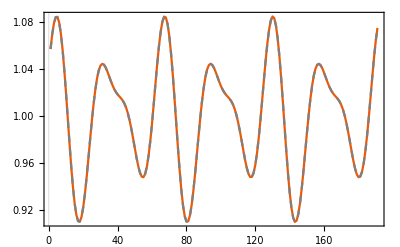

```mathematica
tptsPltTest=Table[tpt,{tpt,1,20,0.1}];

range=Total[Abs[sinCoeffsInitTest]+Abs[cosCoeffsInitTest]]+10^-8
Show[
ListLinePlot[Table[graph[<|"tpt"->{tpt}|>],{tpt,tptsPltTest}]],
ListLinePlot[Table[offsetFixedTest[[1]]+(Sum[sinCoeffsInitTest[[i]]*Sin[freqsTest[[i]]*(tpt-1)]+cosCoeffsInitTest[[i]]*Cos[freqsTest[[i]]*(tpt-1)],{i,Length[freqsTest]}])/Max[range,1],{tpt,tptsPltTest}],PlotStyle->{Gray,Dashed}],
PlotRange->All
]
```

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,offsetFixedTest,graph,tptsPltTest,range]
```

# Inverse of diagonal matrix

## Inverse of diagonal matrix

```mathematica
inverseDiagMatLayer[n_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
If[n>1,
layerDefns["nil"]=NetArrayLayer["Array"->{0.0},LearningRateMultipliers->None];
];
layerDefns["catenate"]=CatenateLayer[];
layerDefns["reshape"]=ReshapeLayer[{n,n}];
Do[
layerDefns["inv"<>ToString[i]]=ElementwiseLayer[#^-1&];
layerDefns["part"<>ToString[i]]=PartLayer[{i,i}];
layerDefns["reshape"<>ToString[i]]=ReshapeLayer[{1}];
,{i,n}];

layerConn={};
Do[
Do[
If[i==j,
AppendTo[layerConn,("part"<>ToString[i])->("inv"<>ToString[i])->("reshape"<>ToString[i])->"catenate"],
AppendTo[layerConn,"nil"->"catenate"]
]
,{j,n}];
,{i,n}];
AppendTo[layerConn,"catenate"->"reshape"];

Return[NetGraph[layerDefns,layerConn,"Input"->{n,n}]]
];
```

## Test

```mathematica
testMat=DiagonalMatrix[{5,6}]//N;
layer=inverseDiagMatLayer[2];

layer[testMat]
Inverse[testMat]
```

{{0.2,0.},{0.,0.166667}}

{{0.2,0.},{0.,0.166667}}

```mathematica
Clear[testMat,layer]
```

# Convert params layer

## Convert b

```mathematica
convertbLayer[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[#b1+Flatten[Transpose[#wt1].#muh1]-Transpose[#wt1].Sqrt[#varh1].Sqrt[#invvarh2].#muh2&,"b1"->nv,"wt1"->{nh,nv},"muh1"->nh,"varh1"->{nh,nh},"muh2"->nh,"invvarh2"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
b1Test={1,2,3};
wt1Test={{3,4,5},{6,7,8}};
muh1Test={3,4};
varh1Test={{3,0},{0,2}};
varh2Test={{5,0},{0,6}};
muh2Test={2,8};
b2True=b1Test+Transpose[wt1Test].muh1Test-Transpose[wt1Test].Sqrt[varh1Test].Inverse[Sqrt[varh2Test]].muh2Test//N
b2Actual=convertbLayer[3,2][<|
"b1"->b1Test,
"wt1"->wt1Test,
"muh1"->muh1Test,
"varh1"->varh1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{1.63961,3.47161,5.30362}

{1.63961,3.47161,5.30362}

```mathematica
Clear[b1Test,wt1Test,muh1Test,varh1Test,varh2Test,muh2Test,b2True,b2Actual]
```

## Convert wt

```mathematica
convertwtLayer[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[Sqrt[#invvarh2].Sqrt[#varh1].#wt1&,"invvarh2"->{nh,nh},"wt1"->{nh,nv},"varh1"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
wt1Test={{3,4,5},{6,7,8}};
varh1Test={{3,0},{0,4}};
varh2Test={{5,0},{0,6}};
wt2True=Inverse[Sqrt[varh2Test]].Sqrt[varh1Test].wt1Test//N
wt2Actual=convertwtLayer[3,2][<|
"wt1"->wt1Test,
"varh1"->varh1Test,
"varh2"->varh2Test
|>]
```

{{2.32379,3.09839,3.87298},{4.89898,5.71548,6.53197}}

{{2.32379,3.09839,3.87298},{4.89898,5.71548,6.53197}}

```mathematica
Clear[wt1Test,varh1Test,varh2Test,wt2True,wt2Actual]
```

## Convert b from 0

```mathematica
convertbLayerFrom0[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[#b1-Transpose[#wt1].Sqrt[#invvarh2].#muh2&,"b1"->nv,"wt1"->{nh,nv},"invvarh2"->{nh,nh},"muh2"->nh],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
];
```

## Test

```mathematica
b1Test={1,2,3};
wt1Test={{3,4,5},{6,7,8}};
varh2Test=DiagonalMatrix[{5,6}];
muh2Test={2,8};
b2True=b1Test-Transpose[wt1Test].Sqrt[Inverse[varh2Test]].muh2Test//N
layer=convertbLayerFrom0[3,2]
b2Actual=layer[<|
"b1"->b1Test,
"wt1"->wt1Test,
"varh2"->varh2Test,
"muh2"->muh2Test
|>]
```

{-21.2792,-24.4396,-27.6}

NetGraph[<>]

{-21.2792,-24.4396,-27.6}

```mathematica
Clear[b1Test,wt1Test,varh2Test,muh2Test,b2True,layer,b2Actual]
```

## Convert wt from 0

```mathematica
convertwtLayerFrom0[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"fn"->FunctionLayer[Sqrt[#invvarh2].#wt1&,"wt1"->{nh,nv},"invvarh2"->{nh,nh}],
"invvarh2"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh2"]->"invvarh2"->NetPort["fn","invvarh2"]
};
Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
wt1Test={{3,4,5},{6,7,8}};
varh2Test={{5,0},{0,8}};
wt2True=Inverse[Sqrt[varh2Test]].wt1Test//N
wt2Actual=convertwtLayerFrom0[3,2][<|
"wt1"->wt1Test,
"varh2"->varh2Test
|>]
```

{{1.34164,1.78885,2.23607},{2.12132,2.47487,2.82843}}

{{1.34164,1.78885,2.23607},{2.12132,2.47487,2.82843}}

```mathematica
Clear[wt1Test,varh2Test,wt2True,wt2Actual]
```

# Make convert params0 to params layer

## Fourier graph for muh

```mathematica
makeFourierGraphMuh[nh_,freqs_,sinCoeffsInit_,cosCoeffsInit_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
layerDefns["catenate"]=CatenateLayer[];

Do[
layerDefns["muh"<>ToString[i]]=makeFourierGraph[freqs,sinCoeffsInit,cosCoeffsInit,{0}];
layerDefns["muh"<>ToString[i]<>"Reshape"]=ReshapeLayer[{1}];
,{i,nh}];

layerConn={};

Do[
AppendTo[layerConn,"muh"<>ToString[i]->"muh"<>ToString[i]<>"Reshape"->"catenate"];
,{i,nh}];

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
freqsTest={1,2,3};
sinCoeffsInitTest={1.0,2.0,3.0};
cosCoeffsInitTest={1.0,2.0,3.0};
nhTest=2;
layer=makeFourierGraphMuh[nhTest,freqsTest,sinCoeffsInitTest,cosCoeffsInitTest]
tptTest=4;
layer[tptTest]
```

NetGraph[<>]

{-0.0820332,-0.0820332}

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,nhTest,layer,tptTest]
```

## Fourier graph for varh

```mathematica
makeFourierGraphVarh[nh_,freqs_,sinCoeffsInit_,cosCoeffsInit_]:=Module[
{layerDefns,layerConn}
,
layerDefns=Association[];
layerDefns["catenate"]=CatenateLayer[];
If[nh>1,
layerDefns["nil"]=NetArrayLayer[Array->{0.0},LearningRateMultipliers->None];
];
layerDefns["reshape"]=ReshapeLayer[{nh,nh}];

Do[
layerDefns["varhDiag"<>ToString[i]]=makeFourierGraph[freqs,sinCoeffsInit,cosCoeffsInit,{1.01}];
layerDefns["varhDiag"<>ToString[i]<>"Reshape"]=ReshapeLayer[{1}];
,{i,nh}];

layerConn={};

Do[
Do[
If[i==j,
AppendTo[layerConn,"varhDiag"<>ToString[i]->"varhDiag"<>ToString[i]<>"Reshape"->"catenate"],
AppendTo[layerConn,"nil"->"catenate"]
]
,{j,nh}];
,{i,nh}];
AppendTo[layerConn,"catenate"->"reshape"];

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
freqsTest={1,2,3};
sinCoeffsInitTest={1.0,2.0,3.0};
cosCoeffsInitTest={1.0,2.0,3.0};
nhTest=2;
layer=makeFourierGraphVarh[nhTest,freqsTest,sinCoeffsInitTest,cosCoeffsInitTest]
tptTest=3;
layer[tptTest]//MatrixForm
```

NetGraph[<>]

(0.98621 | 0.
0. | 0.98621)

```mathematica
Clear[freqsTest,sinCoeffsInitTest,cosCoeffsInitTest,nhTest,layer,tptTest]
```

## Convert params 0 to params

```mathematica
makeConvertParams0ToParamsLayer[nv_,nh_,freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_]:=Module[
{layerDefns,layerConn,graph}
,
layerDefns=<|
"layerMuh"->makeFourierGraphMuh[nh,freqs,muhSinCoeffsInit,muhCosCoeffsInit],
"layerVarh"->makeFourierGraphVarh[nh,freqs,varhSinCoeffsInit,varhCosCoeffsInit],

"convertblayer"->convertbLayerFrom0[nv,nh],
"flattenb"->FlattenLayer[],
"convertwtlayer"->convertwtLayerFrom0[nv,nh]
|>;

layerConn={
NetPort["tpt"]->NetPort["layerMuh","tpt"],
NetPort["tpt"]->NetPort["layerVarh","tpt"],

"layerMuh"->NetPort["convertblayer","muh2"],
"layerVarh"->NetPort["convertblayer","varh2"],
"convertblayer"->"flattenb"->NetPort["b2"],

"layerVarh"->NetPort["convertwtlayer","varh2"],
"convertwtlayer"->NetPort["wt2"],

"layerMuh"->NetPort["muh2"],
"layerVarh"->NetPort["varh2"],
NetPort["sig2"]->NetPort["sig2"]
};

graph=NetGraph[layerDefns,layerConn,"sig2"->1];
Return[graph]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
freqsTest={0.1,0.2,0.3,0.4};
muhCosCoeffsInitTest=ConstantArray[0,4];
muhSinCoeffsInitTest=ConstantArray[0,4];
varhCosCoeffsInitTest=ConstantArray[0,4];varhSinCoeffsInitTest=ConstantArray[0,4];
```

```mathematica
makeConvertParams0ToParamsLayer[nvTest,nhTest,freqsTest,muhCosCoeffsInitTest,muhSinCoeffsInitTest,varhCosCoeffsInitTest,varhSinCoeffsInitTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest,freqsTest,muhCosCoeffsInitTest,muhSinCoeffsInitTest,varhCosCoeffsInitTest,varhSinCoeffsInitTest]
```

# Moments from params

## Catenate varv, varvh, varh

```mathematica
makeVarArrayReshapeLayer[nv_,nh_]:=FunctionLayer[Transpose[Catenate[{Transpose[Catenate[{#varv,#varvh}]],Transpose[Catenate[{Transpose[#varvh],#varh}]]}]]&,"varv"->{nv,nv},"varvh"->{nh,nv},"varh"->{nh,nh}]
```

## Test

```mathematica
lyr=makeVarArrayReshapeLayer[nv,nh]

varvTest=RandomReal[{-1,1},{nv,nv}];
varvhTest=RandomReal[{-1,1},{nh,nv}];
varhTest=RandomReal[{-1,1},{nh,nh}];
ArrayFlatten[{{varvTest,Transpose[varvhTest]},{varvhTest,varhTest}}]

lyr[<|
"varv"->varvTest,
"varvh"->varvhTest,
"varh"->varhTest
|>]
```

FunctionLayer[<>]

{{-0.251314,-0.974586,0.533101,0.535995,0.414617},{-0.648598,0.0126903,-0.450741,-0.620368,-0.405434},{0.909966,0.124046,-0.365528,0.697705,-0.840767},{0.535995,-0.620368,0.697705,0.588554,-0.319566},{0.414617,-0.405434,-0.840767,-0.0413284,-0.846731}}

{{-0.251314,-0.974586,0.533101,0.535995,0.414617},{-0.648598,0.0126903,-0.450741,-0.620368,-0.405434},{0.909966,0.124046,-0.365528,0.697705,-0.840767},{0.535995,-0.620368,0.697705,0.588553,-0.319566},{0.414617,-0.405434,-0.840767,-0.0413284,-0.846731}}

```mathematica
Clear[lyr,varvTest,varvhTest,varhTest]
```

## Convert params to moments

```mathematica
makeGraphConvertParamsToMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"varvh"->FunctionLayer[#varh.#wt&,"varh"->{nh,nh},"wt"->{nh,nv}],
"idmat"->NetArrayLayer["Array"->IdentityMatrix[nv],LearningRateMultipliers->None],
"varv"->FunctionLayer[Transpose[#wt].#varh.#wt+#sig2*#idmat&,"wt"->{nh,nv},"varh"->{nh,nh},"sig2"->1,"idmat"->{nv,nv}],
"muv"->FunctionLayer[#b+Transpose[#wt].#muh&,"b"->nv,"wt"->{nh,nv},"muh"->nh],

"mu"->FunctionLayer[Catenate[{#muv,#muh}]&,"muv"->nv,"muh"->nh],
"var"->makeVarArrayReshapeLayer[nv,nh]
|>;

layerConn={
(* varvh *)
NetPort["varh"]->NetPort["varvh","varh"],
NetPort["wt"]->NetPort["varvh","wt"],

(* varv *)
NetPort["wt"]->NetPort["varv","wt"],
NetPort["varh"]->NetPort["varv","varh"],
NetPort["sig2"]->NetPort["varv","sig2"],
"idmat"->NetPort["varv","idmat"],

(* muv *)
NetPort["b"]->NetPort["muv","b"],
NetPort["wt"]->NetPort["muv","wt"],
NetPort["muh"]->NetPort["muv","muh"],

(* mu *)
"muv"->NetPort["mu","muv"],
NetPort["muh"]->NetPort["mu","muh"],
"mu"->NetPort["mu"],

(* var *)
"varvh"->NetPort["var","varvh"],
"varv"->NetPort["var","varv"],
NetPort["varh"]->NetPort["var","varh"],
"var"->NetPort["var"],

(* Misc *)
"varvh"->NetPort["varvh"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
nvTest=3;
nhTest=2;
makeGraphConvertParamsToMoments[nvTest,nhTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

# NMoments from moments/params

## Convert moments to nmoments

```mathematica
makeGraphConvertMomentsToNMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"reshapeMu"->ReshapeLayer[{nv+nh,1}],
"kpv"->FunctionLayer[#mu.Transpose[#mu]&,"mu"->{nv+nh,1}],
"nvar"->TotalLayer[]
|>;

layerConn={
NetPort["mu"]->"reshapeMu"->"kpv"->"nvar",
NetPort["var"]->"nvar",
NetPort["mu"]->NetPort["mu"],
"nvar"->NetPort["nvar"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
makeGraphConvertMomentsToNMoments[nvTest,nhTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

## Convert params to nmoments

```mathematica
makeGraphConvertParamsToNMoments[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"paramsToMoments"->makeGraphConvertParamsToMoments[nv,nh],
"momentsToNMoments"->makeGraphConvertMomentsToNMoments[nv,nh]
|>;

layerConn={
NetPort["paramsToMoments","mu"]->NetPort["momentsToNMoments","mu"],
NetPort["paramsToMoments","var"]->NetPort["momentsToNMoments","var"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
makeGraphConvertParamsToNMoments[nvTest,nhTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

# Death rxn

```mathematica
makeDeathMeans[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"f"->FunctionLayer[-#mu[[iSp]]*UnitVector[nv+nh,iSp]&,"mu"->(nv+nh)]
|>;
layerConn={"f"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeUnitMat[nv_,nh_,i0_,j0_]:=NetArrayLayer["Array"->Table[If[i==i0&&j==j0,1,0],{i,nv+nh},{j,nv+nh}],LearningRateMultipliers->None]
```

```mathematica
makeUnitMatSymm[nv_,nh_,i0_,j0_]:=NetArrayLayer["Array"->Table[If[(i==i0&&j==j0)||(i==j0&&j==i0),1,0],{i,nv+nh},{j,nv+nh}],LearningRateMultipliers->None]
```

```mathematica
makeDeathNVarDiagMat[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[nv,nh,iSp,iSp],
"mult"->FunctionLayer[#unitMat*(-2*#nvar[[iSp,iSp]]+#mu[[iSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeDeathNVarOffDiagMatSymm[nv_,nh_,iSp_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[nv,nh,iSp,jSp],
"mult"->FunctionLayer[#unitMat*(-#nvar[[iSp,jSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeDeathNVar[nv_,nh_,iSp_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

layerName="m"<>ToString[iSp]<>ToString[iSp];
layerDefns[layerName]=makeDeathNVarDiagMat[nv,nh,iSp];
AppendTo[layerNames,layerName];

Do[
If[iSp==jSp,Continue[]];
layerName="m"<>ToString[iSp]<>ToString[jSp];
layerDefns[layerName]=makeDeathNVarOffDiagMatSymm[nv,nh,iSp,jSp];
AppendTo[layerNames,layerName];
,{jSp,nv+nh}];

layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

## Test

```mathematica
makeRxnDeathNMomentsTE[nMoments_,iSp_]:=Module[
{nv,nh,te,mu,nvar,n}
,
n=3;

(* Means *)
mu=ConstantArray[0,n];
mu[[iSp]]=-nMoments["mu"][[iSp]];

(* Variances *)
nvar=ConstantArray[0,{n,n}];
nvar[[iSp,iSp]]=-2*nMoments["nvar"][[iSp,iSp]]+nMoments["mu"][[iSp]];
Do[
If[iSp==jSp,Continue[]];
nvar[[iSp,jSp]]=-nMoments["nvar"][[iSp,jSp]];
nvar[[jSp,iSp]]=nvar[[iSp,jSp]];
,{jSp,n}];

te=Association[];
te["muTE"]=mu;
te["nvarTE"]=nvar;

Return[te]
]
```

```mathematica
nMoments=Association[];
nMoments["nvar"]=RandomReal[{-1,1},{3,3}];
nMoments["mu"]=RandomReal[{-1,1},3];
nv=2;
nh=1;
outTrue=makeRxnDeathNMomentsTE[nMoments,2];

lyr=makeDeathMeans[nv,nh,2];
muTrue=outTrue["muTE"]
muTest=lyr[nMoments]
Max[Abs[muTest-muTrue]]<10^-5

lyr=makeDeathNVar[nv,nh,2];
nvarTrue=outTrue["nvarTE"]
nvarTest=lyr[nMoments]
Max[Abs[nvarTest-nvarTrue]]<10^-5
```

{0,0.73543,0}

{0.,0.73543,0.}

True

{{0,-0.630374,0},{-0.630374,-0.892287,-0.220911},{0,-0.220911,0}}

{{0.,-0.630374,0.},{-0.630374,-0.892287,-0.220911},{0.,-0.220911,0.}}

True

# Birth rxn

```mathematica
makeBirthMeans[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"f"->FunctionLayer[#mu[[iSp]]*UnitVector[nv+nh,iSp]&,"mu"->(nv+nh)]
|>;
layerConn={"f"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVarDiagMat[nv_,nh_,iSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[nv,nh,iSp,iSp],
"mult"->FunctionLayer[#unitMat*(2*#nvar[[iSp,iSp]]+#mu[[iSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVarOffDiagMatSymm[nv_,nh_,iSp_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[nv,nh,iSp,jSp],
"mult"->FunctionLayer[#unitMat*(#nvar[[iSp,jSp]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeBirthNVar[nv_,nh_,iSp_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

layerName="m"<>ToString[iSp]<>ToString[iSp];
layerDefns[layerName]=makeBirthNVarDiagMat[nv,nh,iSp];
AppendTo[layerNames,layerName];

Do[
If[iSp==jSp,Continue[]];
layerName="m"<>ToString[iSp]<>ToString[jSp];
layerDefns[layerName]=makeBirthNVarOffDiagMatSymm[nv,nh,iSp,jSp];
AppendTo[layerNames,layerName];
,{jSp,nv+nh}];

layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

## Test

```mathematica
makeRxnBirthNMomentsTE[nMoments_,iSp_]:=Module[
{nv,nh,te,mu,nvar,n}
,
n=3;

(* Means *)
mu=ConstantArray[0,n];
mu[[iSp]]=nMoments["mu"][[iSp]];

(* Variances *)
nvar=ConstantArray[0,{n,n}];
nvar[[iSp,iSp]]=2*nMoments["nvar"][[iSp,iSp]]+nMoments["mu"][[iSp]];
Do[
If[iSp==jSp,Continue[]];
nvar[[iSp,jSp]]=nMoments["nvar"][[iSp,jSp]];
nvar[[jSp,iSp]]=nvar[[iSp,jSp]];
,{jSp,n}];

te=Association[];
te["muTE"]=mu;
te["nvarTE"]=nvar;

Return[te]
]
```

```mathematica
nMoments=Association[];
nMoments["nvar"]=RandomReal[{-1,1},{3,3}];
nMoments["mu"]=RandomReal[{-1,1},3];
nv=2;
nh=1;
outTrue=makeRxnBirthNMomentsTE[nMoments,1];

lyr=makeBirthMeans[nv,nh,1];
muTrue=outTrue["muTE"]
muTest=lyr[nMoments]
Max[Abs[muTest-muTrue]]<10^-5

lyr=makeBirthNVar[nv,nh,1];
nvarTrue=outTrue["nvarTE"]
nvarTest=lyr[nMoments]
Max[Abs[nvarTest-nvarTrue]]<10^-5
```

{0.733005,0,0}

{0.733005,0.,0.}

True

{{1.13147,0.999316,-0.819578},{0.999316,0,0},{-0.819578,0,0}}

{{1.13147,0.999316,-0.819578},{0.999316,0.,0.},{-0.819578,0.,0.}}

True

# Eat rxn

```mathematica
makeEatMeans[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"prey"->FunctionLayer[-#nvar[[iHunter,iPrey]]*UnitVector[nv+nh,iPrey]&,"nvar"->{nv+nh,nv+nh}],
"hunter"->FunctionLayer[#nvar[[iHunter,iPrey]]*UnitVector[nv+nh,iHunter]&,"nvar"->{nv+nh,nv+nh}],
"total"->TotalLayer[]
|>;
layerConn={{"hunter","prey"}->"total"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeNMoment3[nv_,nh_,i_,j_,k_]:=FunctionLayer[
-2.0*#mu[[i]]*#mu[[j]]*#mu[[k]]+#mu[[i]]*#nvar[[j,k]]+#mu[[j]]*#nvar[[i,k]]+#mu[[k]]*#nvar[[i,j]]&
,"mu"->nv+nh
,"nvar"->{nv+nh,nv+nh}]
```

```mathematica
makeEatNVarPreyPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[nv,nh,iPrey,iPrey],
"n3"->makeNMoment3[nv,nh,iPrey,iPrey,iHunter],
"mult"->FunctionLayer[#unitMat*(-2.0*#n3+#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarHunterHunter[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[nv,nh,iHunter,iHunter],
"n3"->makeNMoment3[nv,nh,iHunter,iHunter,iPrey],
"mult"->FunctionLayer[#unitMat*(2.0*#n3+#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarHunterPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[nv,nh,iHunter,iPrey],
"n3hhp"->makeNMoment3[nv,nh,iHunter,iHunter,iPrey],
"n3hpp"->makeNMoment3[nv,nh,iHunter,iPrey,iPrey],
"mult"->FunctionLayer[#unitMat*(-#n3hhp+#n3hpp-#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3hhp"->NetPort["mult","n3hhp"],
"n3hpp"->NetPort["mult","n3hpp"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVarLoop[nv_,nh_,iHunter_,iPrey_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMatPrey"->makeUnitMatSymm[nv,nh,iPrey,jSp],
"unitMatHunter"->makeUnitMatSymm[nv,nh,iHunter,jSp],
"n3"->makeNMoment3[nv,nh,jSp,iPrey,iHunter],
"mult"->FunctionLayer[-#unitMatPrey*#n3+#unitMatHunter*#n3&]
|>;

layerConn={
"unitMatPrey"->NetPort["mult","unitMatPrey"],
"unitMatHunter"->NetPort["mult","unitMatHunter"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeEatNVar[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

(* Prey-prey *)
layerName="m"<>ToString[iPrey]<>ToString[iPrey];
layerDefns[layerName]=makeEatNVarPreyPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Hunter-hunter *)
layerName="m"<>ToString[iHunter]<>ToString[iHunter];
layerDefns[layerName]=makeEatNVarHunterHunter[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Hunter-prey *)
layerName="m"<>ToString[iHunter]<>ToString[iPrey];
layerDefns[layerName]=makeEatNVarHunterPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Loop *)
Do[
If[
iPrey!=jSp&&iHunter!=jSp,

layerName="d"<>ToString[jSp];
layerDefns[layerName]=makeEatNVarLoop[nv,nh,iHunter,iPrey,jSp];
AppendTo[layerNames,layerName];
];
,{jSp,nv+nh}];

(* Sum *)
layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

# Eat Ann rxn

```mathematica
makeAnnMeans[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"prey"->FunctionLayer[-#nvar[[iHunter,iPrey]]*UnitVector[nv+nh,iPrey]&,"nvar"->{nv+nh,nv+nh}],
"total"->TotalLayer[]
|>;
layerConn={"prey"->"total"->NetPort["muTE"]};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeNMoment3[nv_,nh_,i_,j_,k_]:=FunctionLayer[
-2.0*#mu[[i]]*#mu[[j]]*#mu[[k]]+#mu[[i]]*#nvar[[j,k]]+#mu[[j]]*#nvar[[i,k]]+#mu[[k]]*#nvar[[i,j]]&
,"mu"->nv+nh
,"nvar"->{nv+nh,nv+nh}]
```

```mathematica
makeAnnNVarPreyPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMat[nv,nh,iPrey,iPrey],
"n3"->makeNMoment3[nv,nh,iPrey,iPrey,iHunter],
"mult"->FunctionLayer[#unitMat*(-2.0*#n3+#nvar[[iHunter,iPrey]])&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeAnnNVarHunterPrey[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMat"->makeUnitMatSymm[nv,nh,iHunter,iPrey],
"n3hhp"->makeNMoment3[nv,nh,iHunter,iHunter,iPrey],
"mult"->FunctionLayer[#unitMat*(-#n3hhp)&]
|>;

layerConn={
"unitMat"->NetPort["mult","unitMat"],
"n3hhp"->NetPort["mult","n3hhp"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeAnnNVarLoop[nv_,nh_,iHunter_,iPrey_,jSp_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"unitMatPrey"->makeUnitMatSymm[nv,nh,iPrey,jSp],
"n3"->makeNMoment3[nv,nh,jSp,iPrey,iHunter],
"mult"->FunctionLayer[-#unitMatPrey*#n3&]
|>;

layerConn={
"unitMatPrey"->NetPort["mult","unitMatPrey"],
"n3"->NetPort["mult","n3"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeAnnNVar[nv_,nh_,iHunter_,iPrey_]:=Module[
{layerDefns,layerName,layerNames,layerConn}
,
layerNames={};
layerDefns=Association[];

(* Prey-prey *)
layerName="m"<>ToString[iPrey]<>ToString[iPrey];
layerDefns[layerName]=makeAnnNVarPreyPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Hunter-prey *)
layerName="m"<>ToString[iHunter]<>ToString[iPrey];
layerDefns[layerName]=makeAnnNVarHunterPrey[nv,nh,iHunter,iPrey];
AppendTo[layerNames,layerName];

(* Loop *)
Do[
If[
iPrey!=jSp&&iHunter!=jSp,

layerName="d"<>ToString[jSp];
layerDefns[layerName]=makeAnnNVarLoop[nv,nh,iHunter,iPrey,jSp];
AppendTo[layerNames,layerName];
];
,{jSp,nv+nh}];

(* Sum *)
layerDefns["tot"]=TotalLayer[];

layerConn={layerNames->"tot"->NetPort["nvarTE"]};

Return[NetGraph[layerDefns,layerConn,"nvar"->{nv+nh,nv+nh},"mu"->nv+nh]]
]
```

# Convert NMomentsTE to MomentsTE

```mathematica
makeConvertNMomentsTEtoMomentsTE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"reshapeMu"->ReshapeLayer[{nv+nh,1}],
"reshapeMuTE"->ReshapeLayer[{nv+nh,1}],
"negkpv"->FunctionLayer[-#muTE.Transpose[#mu]-#mu.Transpose[#muTE]&,"mu"->{nv+nh,1},"muTE"->{nv+nh,1}],
"varTE"->TotalLayer[]
|>;

layerConn={
NetPort["mu"]->"reshapeMu"->NetPort["negkpv","mu"],
NetPort["muTE"]->"reshapeMuTE"->NetPort["negkpv","muTE"],
{NetPort["nvarTE"],"negkpv"}->"varTE"->NetPort["varTE"],
NetPort["muTE"]->NetPort["muTEout"]
};

Return[NetGraph[layerDefns,layerConn,"muTE"->nv+nh,"mu"->nv+nh]]
]
```

## Test

```mathematica
convertNMomentsTEtoMomentsTE[moments_,rxnNMomentsTE_]:=Module[
{rxnMomentsTE,kpv}
,
rxnMomentsTE=Association[];
rxnMomentsTE["muTE"]=rxnNMomentsTE["muTE"];

kpv=KroneckerProduct[rxnNMomentsTE["muTE"],moments["mu"]]+KroneckerProduct[moments["mu"],rxnNMomentsTE["muTE"]];
rxnMomentsTE["varTE"]=rxnNMomentsTE["nvarTE"]-kpv;

Return[rxnMomentsTE];
]
```

```mathematica
moments=<|
"mu"->RandomReal[{-1,1},nv+nh]
|>;
x=RandomReal[{-1,1},{nv+nh,nv+nh}];
rxnNMomentsTE=<|
"muTE"->RandomReal[{-1,1},nv+nh],
"nvarTE"->x+Transpose[x]
|>;
momentsTEtrue=convertNMomentsTEtoMomentsTE[moments,rxnNMomentsTE]
momentsTEtest=makeConvertNMomentsTEtoMomentsTE[nv,nh][Join[moments,rxnNMomentsTE]]

Max[Abs[Flatten[Values[momentsTEtrue]]-Flatten[Values[momentsTEtest]]]]<10^-5
```

<|muTE→{0.0171337,-0.86167,-0.220535,-0.164839,0.0888936},varTE→{{1.12889,0.980837,0.890431,0.855915,0.741501},{0.980837,-1.68452,-0.270711,0.740451,1.08514},{0.890431,-0.270711,-0.159521,1.2237,-0.627137},{0.855915,0.740451,1.2237,1.85696,-0.0592952},{0.741501,1.08514,-0.627137,-0.0592952,-1.61261}}|>

<|muTEout→{0.0171337,-0.86167,-0.220535,-0.164839,0.0888936},varTE→{{1.12889,0.980837,0.890431,0.855915,0.741501},{0.980837,-1.68452,-0.270711,0.740451,1.08514},{0.890431,-0.270711,-0.159521,1.2237,-0.627137},{0.855915,0.740451,1.2237,1.85696,-0.0592952},{0.741501,1.08514,-0.627137,-0.0592952,-1.61261}}|>

True

# Convert MomentsTE to ParamMomentsTE

```mathematica
makeConvertMomentsTEtoParamMomentsTE[nv_,nh_]:=Module[
{layerDefns,name,layerConn}
,
layerDefns=<|
"muvTE"->PartLayer[1;;nv],
"muhTE"->PartLayer[nv+1;;],
"varvhTE"->PartLayer[{nv+1;;,;;nv}],
"varvbarTEpart"->PartLayer[{;;nv,;;nv}],
"varvbarTEdiagsum"->makeSumDiagonal[nv],
"varhTE"->PartLayer[{nv+1;;,nv+1;;}]
|>;

layerConn={
NetPort["muTE"]->"muvTE"->NetPort["muvTE"],
NetPort["muTE"]->"muhTE"->NetPort["muhTE"],

NetPort["varTE"]->"varvhTE"->NetPort["varvhTE"],
NetPort["varTE"]->"varhTE"->NetPort["varhTE"],
NetPort["varTE"]->"varvbarTEpart"->"varvbarTEdiagsum"->NetPort["varvbarTE"]
};

Return[NetGraph[layerDefns,layerConn,"varTE"->{nv+nh,nv+nh},"muvTE"->nv,"muhTE"->nh,"varvbarTE"->"Real","muTE"->(nv+nh)]]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
makeConvertMomentsTEtoParamMomentsTE[nvTest,nhTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

# Convert ParamMomentsTE to ParamsTE

```mathematica
makeSumDiagonal[n_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"diag"->FunctionLayer[Flatten[#*IdentityMatrix[n]]&],
"tot"->SummationLayer[]
|>;
layerConn={"diag"->"tot"};
Return[NetGraph[layerDefns,layerConn]]
]
```

```mathematica
makeConvertParamMomentsTEtoParamsTE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"bTE"->FunctionLayer[#muvTE-Transpose[#varvhTE].#varhInv.#muh+Transpose[#varvh].#varhInv.#varhTE.#varhInv.#muh-Transpose[#varvh].#varhInv.#muhTE&,"muvTE"->nv,"varvhTE"->{nh,nv},"varhInv"->{nh,nh},"muh"->nh,"varvh"->{nh,nv},"varhTE"->{nh,nh},"muhTE"->nh],
"wtTE"->FunctionLayer[-#varhInv.(#varhTE.#varhInv.#varvh)+#varhInv.#varvhTE&,"varhInv"->{nh,nh},"varhTE"->{nh,nh},"varvh"->{nh,nv},"varvhTE"->{nh,nv}],
"sig2TEmat"->FunctionLayer[Transpose[#varvhTE].#varhInv.#varvh-Transpose[#varvh].#varhInv.(#varhTE.#varhInv.#varvh)+Transpose[#varvh].#varhInv.#varvhTE&,"varvhTE"->{nh,nv},"varhInv"->{nh,nh},"varvh"->{nh,nv},"varhTE"->{nh,nh}],
"sig2TEsumdiag"->makeSumDiagonal[nv],
"sig2TE"->FunctionLayer[#varvbarTE/nv-#sig2TEsumdiag/nv&,"varvbarTE"->"Real","Output"->"Real"],
"varhInv"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["muhTE"]->NetPort["muhTE"],
NetPort["varhTE"]->NetPort["varhTE"],
"sig2TEmat"->"sig2TEsumdiag"->NetPort["sig2TE","sig2TEsumdiag"],
"sig2TE"->NetPort["sig2TE"],
"bTE"->NetPort["bTE"],
"wtTE"->NetPort["wtTE"],
"varhInv"->NetPort["bTE","varhInv"],
"varhInv"->NetPort["wtTE","varhInv"],
"varhInv"->NetPort["sig2TEmat","varhInv"],
NetPort["varh"]->"varhInv"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

```mathematica
makeConvertParamMomentsTEtoParamsTE[nv,nh]
```

NetGraph[<>]

# Convert ParamsTE to Params0TE

```mathematica
makeConvertParamsTEtoParams0TE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"b2TE"->FunctionLayer[#fb1+Transpose[#fwt1].#muh1+Transpose[#wt1].#fmuh1&,"fb1"->nv,"fwt1"->{nh,nv},"muh1"->nh,"wt1"->{nh,nv},"fmuh1"->nh],
"wt2TE"->FunctionLayer[0.5*Sqrt[#varh1Inv].#fvarh1.#wt1+Sqrt[#varh1].#fwt1&,"varh1Inv"->{nh,nh},"fvarh1"->{nh,nh},"wt1"->{nh,nv},"varh1"->{nh,nh},"fwt1"->{nh,nv}],
"varh1Inv"->inverseDiagMatLayer[nh]
|>;

layerConn={
NetPort["varh1"]->"varh1Inv",
"varh1Inv"->NetPort["wt2TE","varh1Inv"],
"b2TE"->NetPort["b2TE"],
"wt2TE"->NetPort["wt2TE"]
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
convertParamsTELatentSpace[params1_,params1TE_,muh2_,varh2_,fmuh2_,fvarh2_]:=Module[
{fb1,fwt1,fmuh1,fvarh1,fb2,muh1,wt1,varh1,fwt2},

fb1=params1TE["fb"];
fwt1=params1TE["fwt"];
fmuh1=params1TE["fmuh"];
fvarh1=params1TE["fvarh"];

muh1=params1["muh"];
wt1=params1["wt"];
varh1=params1["varh"];

fb2=fb1+Transpose[fwt1].muh1+Transpose[wt1].fmuh1-Transpose[fwt1].Sqrt[varh1].Inverse[Sqrt[varh2]].muh2-0.5*Transpose[wt1].Inverse[Sqrt[varh1]].fvarh1.Inverse[Sqrt[varh2]].muh2+0.5*Transpose[wt1].Sqrt[varh1].(Inverse[Sqrt[varh2]]^3).fvarh2.muh2-Transpose[wt1].Sqrt[varh1].Inverse[Sqrt[varh2]].fmuh2;

fwt2=-0.5*(Inverse[Sqrt[varh2]]^3).fvarh2.Sqrt[varh1].wt1+0.5*Inverse[Sqrt[varh2]].Inverse[Sqrt[varh1]].fvarh1.wt1+Inverse[Sqrt[varh2]].Sqrt[varh1].fwt1;

Return[makeParamsTE[fwt2,fb2,params1TE["fsig2"],fmuh2,fvarh2]];
]
```

```mathematica
nvTest=3;
nhTest=2;

params1test=<|
"wt"->RandomReal[{-1,1},{nhTest,nvTest}],
"b"->RandomReal[{-1,1},nvTest],
"muh"->RandomReal[{-1,1},nhTest],
"varh"->DiagonalMatrix[RandomReal[{0,1},nhTest]],
"sig2"->RandomReal[{-1,1}]
|>;
params1TEtest=<|
"fwt"->RandomReal[{-1,1},{nhTest,nvTest}],
"fb"->RandomReal[{-1,1},nvTest],
"fmuh"->RandomReal[{-1,1},nhTest],
"fvarh"->DiagonalMatrix[RandomReal[{-1,1},nhTest]],
"fsig2"->RandomReal[{-1,1}]
|>;
muh2test=ConstantArray[0,nhTest];
varh2test=IdentityMatrix[nhTest];
fmuh2test=ConstantArray[0,nhTest];
fvarh2test=ConstantArray[0,{nhTest,nhTest}];

valsTrue=convertParamsTELatentSpace[params1test,params1TEtest,muh2test,varh2test,fmuh2test,fvarh2test]

convertParamsTEtoParams0TE=makeConvertParamsTEtoParams0TE[nvTest,nhTest];
valsTest=convertParamsTEtoParams0TE[<|
"varh1"->params1test["varh"],
"fvarh1"->params1TEtest["fvarh"],
"wt1"->params1test["wt"],
"fwt1"->params1TEtest["fwt"],
"muh1"->params1test["muh"],
"fmuh1"->params1TEtest["fmuh"],
"fb1"->params1TEtest["fb"]
|>]

valsTrue=Flatten[{valsTrue["fwt"],valsTrue["fb"]}];
valsTest=Flatten[{valsTest["wt2TE"],valsTest["b2TE"]}];
Max[Abs[valsTest-valsTrue]]<10^-6
```

<|fwt→{{-0.416463,-0.359059,0.60344},{-1.12787,0.437793,-0.324057}},fb→{-1.05652,-0.69548,0.350569},fsig2→0.205242,fmuh→{0,0},fvarh→{{0,0},{0,0}}|>

<|b2TE→{-1.05652,-0.69548,0.350569},wt2TE→{{-0.416463,-0.359059,0.60344},{-1.12787,0.437793,-0.324057}}|>

True

```mathematica
Clear[nhTest,nvTest,params1TEtest,muh2test,params1test,varh2test,fmuh2test,fvarh2test,valsTrue,valsTest]
```

# Convert NMomentsTE to ParamsTE

```mathematica
makeConvertNMomentsTEtoParams0TE[nv_,nh_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"convertNMomentsToMomentsTE"->makeConvertNMomentsTEtoMomentsTE[nv,nh],
"convertMomentsTEtoParamMomentsTE"->makeConvertMomentsTEtoParamMomentsTE[nv,nh],
"convertParamMomentsToParamsTE"->makeConvertParamMomentsTEtoParamsTE[nv,nh],
"convertParamsTEtoParams0TE"->makeConvertParamsTEtoParams0TE[nv,nh]
|>;

layerConn={
NetPort["convertNMomentsToMomentsTE","varTE"]->NetPort["convertMomentsTEtoParamMomentsTE","varTE"],
NetPort["convertNMomentsToMomentsTE","muTEout"]->NetPort["convertMomentsTEtoParamMomentsTE","muTE"],

NetPort["convertMomentsTEtoParamMomentsTE","varvhTE"]->NetPort["convertParamMomentsToParamsTE","varvhTE"],
NetPort["convertMomentsTEtoParamMomentsTE","varvbarTE"]->NetPort["convertParamMomentsToParamsTE","varvbarTE"],
NetPort["convertMomentsTEtoParamMomentsTE","varhTE"]->NetPort["convertParamMomentsToParamsTE","varhTE"],
NetPort["convertMomentsTEtoParamMomentsTE","muvTE"]->NetPort["convertParamMomentsToParamsTE","muvTE"],
NetPort["convertMomentsTEtoParamMomentsTE","muhTE"]->NetPort["convertParamMomentsToParamsTE","muhTE"],

NetPort["wt"]->NetPort["convertParamsTEtoParams0TE","wt1"],
NetPort["varh"]->NetPort["convertParamsTEtoParams0TE","varh1"],
NetPort["muh"]->NetPort["convertParamsTEtoParams0TE","muh1"],
NetPort["convertParamMomentsToParamsTE","wtTE"]->NetPort["convertParamsTEtoParams0TE","fwt1"],
NetPort["convertParamMomentsToParamsTE","varhTE"]->NetPort["convertParamsTEtoParams0TE","fvarh1"],
NetPort["convertParamMomentsToParamsTE","muhTE"]->NetPort["convertParamsTEtoParams0TE","fmuh1"],
NetPort["convertParamMomentsToParamsTE","bTE"]->NetPort["convertParamsTEtoParams0TE","fb1"],

NetPort["convertParamsTEtoParams0TE","wt2TE"]->NetPort["wtTE"],
NetPort["convertParamsTEtoParams0TE","b2TE"]->NetPort["bTE"]
};

Return[NetGraph[layerDefns,layerConn]]
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
makeConvertNMomentsTEtoParams0TE[nvTest,nhTest]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

# Rxns

```mathematica
makeRxnParams0TE[nv_,nh_,rxnSpec_]:=Module[
{layerDefns,layerConn,iHunter,iPrey,iSp}
,
layerDefns=<|
"convertNMomentsTEtoParams0TE"->makeConvertNMomentsTEtoParams0TE[nv,nh],
"convertParamsToNMoments"->makeGraphConvertParamsToNMoments[nv,nh]
|>;

layerConn={
"muTE"->NetPort["convertNMomentsTEtoParams0TE","muTE"],
"nvarTE"->NetPort["convertNMomentsTEtoParams0TE","nvarTE"],

NetPort["convertParamsToNMoments","nvar"]->NetPort["nvarTE","nvar"],
NetPort["convertParamsToNMoments","mu"]->NetPort["nvarTE","mu"],

NetPort["convertParamsToNMoments","mu"]->NetPort["convertNMomentsTEtoParams0TE","mu"],
NetPort["convertParamsToNMoments","varvh"]->NetPort["convertNMomentsTEtoParams0TE","varvh"]
};

(* Reaction *)
If[rxnSpec[[1]]=="eat",
iHunter=rxnSpec[[2]];
iPrey=rxnSpec[[3]];

layerDefns["muTE"]=makeEatMeans[nv,nh,iHunter,iPrey];
layerDefns["nvarTE"]=makeEatNVar[nv,nh,iHunter,iPrey];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","nvar"]->NetPort["muTE","nvar"]
];
];

If[rxnSpec[[1]]=="ann",
iHunter=rxnSpec[[2]];
iPrey=rxnSpec[[3]];

layerDefns["muTE"]=makeAnnMeans[nv,nh,iHunter,iPrey];
layerDefns["nvarTE"]=makeAnnNVar[nv,nh,iHunter,iPrey];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","nvar"]->NetPort["muTE","nvar"]
];
];

If[rxnSpec[[1]]=="birth",
iSp=rxnSpec[[2]];

layerDefns["muTE"]=makeBirthMeans[nv,nh,iSp];
layerDefns["nvarTE"]=makeBirthNVar[nv,nh,iSp];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","mu"]->NetPort["muTE","mu"]
];
];

If[rxnSpec[[1]]=="death",
iSp=rxnSpec[[2]];

layerDefns["muTE"]=makeDeathMeans[nv,nh,iSp];
layerDefns["nvarTE"]=makeDeathNVar[nv,nh,iSp];

AppendTo[layerConn,
NetPort["convertParamsToNMoments","mu"]->NetPort["muTE","mu"]
];
];

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
nTest=nvTest+nhTest;
muTest=RandomReal[{100,500},nTest];

varvTest=DiagonalMatrix[RandomReal[{100,200},nvTest]];
varvTest+=RandomReal[{5,10},{nvTest,nvTest}];
varvTest+=Transpose[varvTest];
varvTest*=0.5;

varhTest=DiagonalMatrix[RandomReal[{100,200},nhTest]];
varvhTest=RandomReal[{5,10},{nvTest,nhTest}];
varTest=ArrayFlatten[{{varvTest,varvhTest},{Transpose[varvhTest],varhTest}}]

SymmetricMatrixQ[varTest]
PositiveDefiniteMatrixQ[varTest]

momentsTest=<|
"mu"->muTest,
"var"->varTest
|>//N;
```

{{117.158,8.21923,7.09689,5.13681,7.03184},{8.21923,186.229,5.58044,7.28054,7.3153},{7.09689,5.58044,127.909,8.39229,8.84516},{5.13681,7.28054,8.39229,108.938,0.},{7.03184,7.3153,8.84516,0.,105.819}}

True

True

```mathematica
paramsTest=convertMomentsToParams[momentsTest,nvTest]
momentsTest=convertParamsToMoments[paramsTest];
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramMomentsTest=convertParamsToParamMoments[paramsTest];
nMomentsTest=convertParamsToNMoments[paramsTest];
nMoments3Test=convertParamsToNMoments3[paramsTest];
```

<|sig2→159.483,muh→{267.676,390.183},varh→{{105.906,0.},{0.,183.056}},wt→{{0.0566476,0.0585189,0.0622336},{0.0431189,0.0392358,0.0388303}},b→{180.204,123.973,73.3646}|>

True

```mathematica
makeParams1TEtest[rxnParamsTEtest_]:=<|
"fb"->rxnParamsTEtest["bTE"],
"fwt"->rxnParamsTEtest["wtTE"],
"fmuh"->rxnParamsTEtest["muhTE"],
"fvarh"->rxnParamsTEtest["varhTE"],
"fsig2"->rxnParamsTEtest["sig2TE"]
|>;
```

```mathematica
validateParams0TE[momentsTest_,paramsTest_,paramMomentsTest_,valsCheck_,rxnNMomentsTEtest_,nhTest_]:=Module[
{rxnMomentsTEtest,rxnParamMomentsTEtest,rxnParamsTEtest,params1TEtest,muh2Test,varh2Test,fmuh2Test,err,fvarh2Test,valsTrue}
,
rxnMomentsTEtest=convertNMomentsTEtoMomentsTE[momentsTest,rxnNMomentsTEtest];
rxnParamMomentsTEtest=convertMomentsTEtoParamMomentsTE[paramsTest,rxnMomentsTEtest];
rxnParamsTEtest=convertParamMomentsTEtoParamsTE[paramMomentsTest,rxnParamMomentsTEtest];
params1TEtest=makeParams1TEtest[rxnParamsTEtest];

muh2Test=ConstantArray[0,nhTest];
varh2Test=IdentityMatrix[nhTest];
fmuh2Test=ConstantArray[0,nhTest];
fvarh2Test=ConstantArray[0,{nhTest,nhTest}];
valsTrue=convertParamsTELatentSpace[paramsTest,params1TEtest,muh2Test,varh2Test,fmuh2Test,fvarh2Test];
Print[valsTrue];
Print[valsCheck];

On[Assert];
Assert[Max[Abs[valsCheck["sig2TE"]-valsTrue["fsig2"]]]<10^0];
Assert[Max[Abs[valsCheck["wtTE"]-valsTrue["fwt"]]]<10^0];
Assert[Max[Abs[valsCheck["bTE"]-valsTrue["fb"]]]<10^0];
Off[Assert];

Return[True];
]
```

```mathematica
lyr=makeRxnParams0TE[nvTest,nhTest,{"eat",1,2}];
valsCheck=lyr[paramsTest]

rxnNMomentsTEtest=makeRxnEatNMomentsTE[nMomentsTest,nMoments3Test,1,2];
validateParams0TE[momentsTest,paramsTest,paramMomentsTest,valsCheck,rxnNMomentsTEtest,nhTest]
```

<|sig2TE→15833.,wtTE→{{218.345,-218.345,0.},{203.181,-203.181,0.}},bTE→{32879.1,-32879.1,0.}|>

<|fwt→{{218.115,-218.115,0.},{203.037,-203.037,0.}},fb→{32879.1,-32879.1,0.},fsig2→15833.,fmuh→{0,0},fvarh→{{0,0},{0,0}}|>

<|sig2TE→15833.,wtTE→{{218.345,-218.345,0.},{203.181,-203.181,0.}},bTE→{32879.1,-32879.1,0.}|>

True

```mathematica
lyr=makeRxnParams0TE[nvTest,nhTest,{"birth",1}];
valsCheck=lyr[paramsTest];

rxnNMomentsTEtest=makeRxnBirthNMomentsTE[nMomentsTest,nMoments3Test,1];
validateParams0TE[momentsTest,paramsTest,paramMomentsTest,valsCheck,rxnNMomentsTEtest,nhTest]
```

<|fwt→{{0.582964,0.,0.},{0.583391,0.,0.}},fb→{212.192,0.,0.},fsig2→177.053,fmuh→{0,0},fvarh→{{0,0},{0,0}}|>

<|sig2TE→177.054,wtTE→{{0.58303,0.,0.},{0.583202,0.,0.}},bTE→{212.192,0.,0.}|>

True

```mathematica
lyr=makeRxnParams0TE[nvTest,nhTest,{"death",1}];
valsCheck=lyr[paramsTest];

rxnNMomentsTEtest=makeRxnDeathNMomentsTE[nMomentsTest,nMoments3Test,1];
validateParams0TE[momentsTest,paramsTest,paramMomentsTest,valsCheck,rxnNMomentsTEtest,nhTest]
```

<|fwt→{{-0.582964,0.,0.},{-0.583391,0.,0.}},fb→{-212.192,0.,0.},fsig2→-35.5913,fmuh→{0,0},fvarh→{{0,0},{0,0}}|>

<|sig2TE→-35.5909,wtTE→{{-0.58303,0.,0.},{-0.583202,0.,0.}},bTE→{-212.192,0.,0.}|>

True

```mathematica
Clear[nvTest,nhTest,nTest,muTest,varvTest,varhTest,varvhTest,varTest,momentsTest,valsCheck,rxnNMomentsTEtest,paramsTest,paramMomentsTest,nMomentsTest,nMoments3Test]
```

## Flatten outputs

```mathematica
layerDefnsFlat=<|
"wtFlat"->FlattenLayer[],
"varhFlat"->FlattenLayer[],
"sig2Arr"->ReshapeLayer[{1}],
"cat"->CatenateLayer[]
|>;
```

```mathematica
layerConnFlat={
NetPort["lyr","sig2TE"]->"sig2Arr",
NetPort["lyr","wtTE"]->"wtFlat",
NetPort["lyr","varhTE"]->"varhFlat",
{"wtFlat",NetPort["lyr","bTE"],"sig2Arr",NetPort["lyr","muhTE"],"varhFlat"}->"cat"
};
```

```mathematica
makeRxnParams0TEflat[nv_,nh_,rxnSpec_]:=Module[
{layerDefns,layerConn}
,
layerDefns=<|
"wtFlat"->FlattenLayer[],
"sig2Arr"->ReshapeLayer[{1}],
"cat"->CatenateLayer[],
"lyr"->makeRxnParams0TE[nv,nh,rxnSpec]
|>;

layerConn={
NetPort["lyr","sig2TE"]->"sig2Arr",
NetPort["lyr","wtTE"]->"wtFlat",
{"wtFlat",NetPort["lyr","bTE"],"sig2Arr"}->"cat"
};

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
nvTest=3;
nhTest=2;
makeRxnParams0TEflat[nvTest,nhTest,{"eat",2,1}]
```

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest]
```

# Import package for tests

```mathematica
SetDirectory[NotebookDirectory[]]
Get["funcs_rxns_moms.m"]
```

/Users/oernst/Documents/papers/2021_03_draft/bifurcation_extrapolate_ip3r/package

# Make graph for inputs

```mathematica
makeGraphInputsWOSTD[nv_,nh_,freqs_,muhCosCoeffsInit_,muhSinCoeffsInit_,varhCosCoeffsInit_,varhSinCoeffsInit_,rxnSpecs_]:=Module[
{layerDefns,layerConn,graph,rxnName,idx}
,
layerDefns=<|
"convert0"->makeConvertParams0ToParamsLayer[nv,nh,freqs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit],
"rxnsCatenate"->CatenateLayer[]
|>;

layerConn={
NetPort["wt"]->NetPort["convert0","wt1"],
NetPort["b"]->NetPort["convert0","b1"]
};

(* Reactions *)
idx=1;
Monitor[
Do[
rxnName="rxn"<>ToString[idx];
idx+=1;

layerDefns[rxnName]=makeRxnParams0TEflat[nv,nh,rxnSpec];

layerConn=Join[layerConn,{
NetPort["convert0","wt2"]->NetPort[rxnName,"wt"],
NetPort["convert0","b2"]->NetPort[rxnName,"b"],
NetPort["convert0","sig2"]->NetPort[rxnName,"sig2"],
NetPort["convert0","muh2"]->NetPort[rxnName,"muh"],
NetPort["convert0","varh2"]->NetPort[rxnName,"varh"],
rxnName->"rxnsCatenate"
}];
,{rxnSpec,rxnSpecs}];
,ProgressIndicator[idx,{1,Length[rxnSpecs]}]];

Return[NetGraph[layerDefns,layerConn]];
]
```

## Test

```mathematica
nvTest=3;
momentsTest=<|
"mu"->{3,2,6,8,7},
"var"->{
{9.0,0.2,0.1,0.08,0.07},
{0.2,3.0,0.1,0.08,0.07},
{0.1,0.1,6.0,0.08,0.07},
{0.08,0.08,0.1,8.0,0.0},
{0.07,0.07,0.07,0.0,9.0}
}
|>//N;
PositiveSemidefiniteMatrixQ[momentsTest["var"]]

paramsTest=convertMomentsToParams[momentsTest,nvTest]
momentsTest=convertParamsToMoments[paramsTest]
PositiveSemidefiniteMatrixQ[momentsTest["var"]]
```

True

<|sig2→8.99866,muh→{8.,7.},varh→{{8.,0.},{0.,9.}},wt→{{0.01,0.01,0.0125},{0.00777778,0.00777778,0.00777778}},b→{2.86556,1.86556,5.84556}|>

<|muv→{3.,2.,6.},muh→{8.,7.},varv→{{9.,0.00134444,0.00154444},{0.00134444,9.,0.00154444},{0.00154444,0.00154444,9.00045}},varvh→{{0.08,0.08,0.1},{0.07,0.07,0.07}},varh→{{8.,0.},{0.,9.}},mu→{3.,2.,6.,8.,7.},var→{{9.,0.00134444,0.00154444,0.08,0.07},{0.00134444,9.,0.00154444,0.08,0.07},{0.00154444,0.00154444,9.00045,0.1,0.07},{0.08,0.08,0.1,8.,0.},{0.07,0.07,0.07,0.,9.}}|>

True

```mathematica
nvTest=3;
nhTest=2;
rxnSpecs={
{"eat",2,1},
{"birth",2},
{"death",1}
}
freqsTest={1,2,3,4};
muhCosCoeffsInit=ConstantArray[0,4];
muhSinCoeffsInit=ConstantArray[0,4];
varhCosCoeffsInit=ConstantArray[0,4];
varhSinCoeffsInit=ConstantArray[0,4];

makeGraphInputsWOSTD[nvTest,nhTest,freqsTest,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit,rxnSpecs]
```

{{eat,2,1},{birth,2},{death,1}}

NetGraph[<>]

```mathematica
Clear[nvTest,nhTest,rxnSpecs,muhCosCoeffsInit,muhSinCoeffsInit,varhCosCoeffsInit,varhSinCoeffsInit,paramsTest,momentsTest]
```